## Empirical "Verification"

three dice versus two dice, take the number of sides as a parameter

```mathematica
Timing[
Module[
{Attacker,Defender,Offense,Defense,Trials,AList,DList,AMean,DMean,AStDev,DStDev},
Sides=6;
Rolls=2;
Trials=10000;
AList={};
DList={};
For[h=1,h≤Trials,h++,{
Attacker=0;
Defender=0;
For[i=1,i≤Rolls,i++,{
Offense=Sort[RandomInteger[{1,Sides},3],Greater];
Defense=Sort[RandomInteger[{1,Sides},2],Greater];
For[j=1,j≤2,j++,{
If[Offense[[j]]>Defense[[j]],Defender++,Attacker++];
}];
}];
AppendTo[AList,N[Attacker/Rolls,2]];
AppendTo[DList,N[Defender/Rolls,2]];
}];
AMean=Mean[AList];
AStDev=StandardDeviation[AList];
Print[Sides,"-Sided Dice, ",Rolls," Rolls, ",Trials," Trials"];
Print["  Att loss per roll: ",AMean];
Print["  Stdev            : ",AStDev];
]
]
```

6-Sided Dice, 2 Rolls, 10000 Trials

Att loss per roll: 0.9

Stdev            : 0.6

{8.2082,Null}

```mathematica
stdev[Sides_,Rolls_]:=Module[
{Attacker,Offense,Defense,Trials,AList,AMean,AStDev},
Trials=10000;
AList={};
For[h=1,h≤Trials,h++,{
Attacker=0;
For[i=1,i≤Rolls,i++,{
Offense=Sort[RandomInteger[{1,Sides},3],Greater];
Defense=Sort[RandomInteger[{1,Sides},2],Greater];
For[j=1,j≤2,j++,{
If[Offense[[j]]>Defense[[j]],,Attacker++];
}];
}];
AppendTo[AList,N[Attacker/Rolls,2]];
}];
AStDev=StandardDeviation[AList]
]
```

{155.992,{0.8,0.6,0.5,0.4,0.4,0.3,0.3,0.3,0.3,0.3,0.2,0.2,0.2,0.2,0.2,0.2}}

{157.092,{0.8,0.6,0.5,0.4,0.4,0.3,0.3,0.3,0.3,0.3,0.2,0.2,0.2,0.2,0.2,0.2}}

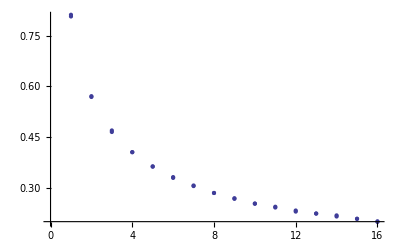

```mathematica
Timing[
FourSides=Table[stdev[4,i],{i,1,16}]
]
Timing[
SixSides=Table[stdev[6,i],{i,1,16}]
]
six=ListPlot[SixSides];
four=ListPlot[FourSides];
Show[four,six]
```

```mathematica
Timing[
Table[stdev[20,i],{i,1,16}]
]
```

{145.85,{0.8,0.6,0.5,0.4,0.4,0.3,0.3,0.3,0.3,0.3,0.2,0.2,0.2,0.2,0.2,0.2}}

```mathematica
Timing[
Table[stdev[6,i],{i,17,24}]
]
```

{105.724,{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2}}

#### Development

```mathematica
Timing[
Module[
{Sides,Attacker,Defender,Offense,Defense,Trials,Rolls,AList,DList},
Sides=20;
Trials=10000;
Rolls=4;
AList={};
DList={};
For[h=1,h≤Trials,h++,{
Attacker=0;
Defender=0;
For[i=1,i≤Rolls,i++,{
Offense=Sort[RandomInteger[{1,Sides},3],Greater];
Defense=Sort[RandomInteger[{1,Sides},2],Greater];
For[j=1,j≤2,j++,{
If[Offense[[j]]>Defense[[j]],Defender++,Attacker++];
}];
}];
AppendTo[AList,Attacker];
AppendTo[DList,Defender];
}];
Print[Sides,"-Sided dice."];
Print[Trials," trials of ",Rolls," rolls each:"];
Print["  Mean attacker loss: ",N[Mean[AList],2]];
Print["  Std dev           : ",N[StandardDeviation[AList],2]];
Print["  Mean defender loss: ",N[Mean[DList],2]];
Print["  Std dev           : ",N[StandardDeviation[DList],2]];
]
]//First
```

20-Sided dice.

10000 trials of 4 rolls each:

Mean attacker loss: 3.

Std dev           : 2.

Mean defender loss: 5.

Std dev           : 2.

3.56423

```mathematica
4.6/5.4//N
```

0.851852

```mathematica
√5//N
```

2.23607

```mathematica
15/27//N
```

0.555556

```mathematica
Timing[
Module[
{Sides,Attacker,Defender,Offense,Defense,Trials,Rolls,Ratios},
Sides=6;
Trials=10000;
Rolls=100;
Ratios={};
For[h=1,h≤Trials,h++,{
Attacker=0;
Defender=0;
For[i=1,i≤Rolls,i++,{
Offense=Sort[RandomInteger[{1,Sides},3],Greater];
Defense=Sort[RandomInteger[{1,Sides},2],Greater];
For[j=1,j≤2,j++,{
If[Offense[[j]]>Defense[[j]],Defender++,Attacker++];
}];
}];
AppendTo[Ratios,N[Attacker/Defender,2]];
}];
Print[Sides,"-Sided dice."];
Print[Trials," trials of ",Rolls," rolls each:"];
Print["  Mean ratio: ",Mean[Ratios]];
Print["  Std dev   : ",StandardDeviation[Ratios]];
]
]//First
```

6-Sided dice.

10000 trials of 100 rolls each:

Mean ratio: 0.9

Std dev   : 0.1

38.4096

## Three dice versus Two dice

### Calculation of risk probabilities for different playing dice.

#### Input

```mathematica
Sides=3;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.242798,0.353909,0.403292}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

1.16049

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

1.38235

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

0.723404

### Save: ∞ sides. Yes, really. I'm not joking. Attacker loses 7/13=0.54 armies per defending army lost.

Somewhere in here I should write up the argument that Cory and I found today. Basic idea: choose five numbers "randomly out of ∞ numbers", order them, then determine which three go to the attacker. There are 5 choose 3 ways to do this, or 10. Diagram each, with "x" standing for attacker's dice, and - standing for the defenders. The key is that each diagram is equally likely. Assign each diagram a score based on how many "wins" it gives to the attacker.That is, 
  x x x - -	0
  x x - x -	0
  x x - - x	1
  x - x x -	1
  x - - x x	2
  x - x - x	2
  - x x x -	1
  - x x - x	2
  - x - x x	2
  - - x x x	2
  Since each diagram is equally like, the expected value of wins is 2(5/10) + 1(3/10) + 0(2/10) = 13/10. Thus in the limit as the number of sides goes to ∞, the attacker expects 13/10 wins per roll. 
  
  The attacker's expected losses per roll is 7/10, and the defender's expected losses per roll is 13/10. The ratio of the two numbers gives an expected value of attacker's losses per defender's loss of 7/13.

### Save: 60 sides. Just for fun. Attacker loses 0.56 armies per defending army lost.

#### Input

```mathematica
Sides=60;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
Print[N[100/Sides d1],"% done"]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

1.66667% done

3.33333% done

5.% done

6.66667% done

8.33333% done

10.% done

11.6667% done

13.3333% done

15.% done

16.6667% done

18.3333% done

20.% done

21.6667% done

23.3333% done

25.% done

26.6667% done

28.3333% done

30.% done

31.6667% done

33.3333% done

35.% done

36.6667% done

38.3333% done

40.% done

41.6667% done

43.3333% done

45.% done

46.6667% done

48.3333% done

50.% done

51.6667% done

53.3333% done

55.% done

56.6667% done

58.3333% done

60.% done

61.6667% done

63.3333% done

65.% done

66.6667% done

68.3333% done

70.% done

71.6667% done

73.3333% done

75.% done

76.6667% done

78.3333% done

80.% done

81.6667% done

83.3333% done

85.% done

86.6667% done

88.3333% done

90.% done

91.6667% done

93.3333% done

95.% done

96.6667% done

98.3333% done

100.% done

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.487455,0.304119,0.208426}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.720971

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.563686

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.77404

### Save: 40 sides. Just for fun. Attacker loses 0.58 armies per defending army lost.

#### Input

```mathematica
Sides=40;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
Print[100/Sides d1,"% done"]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

5/2% done

5% done

15/2% done

10% done

25/2% done

15% done

35/2% done

20% done

45/2% done

25% done

55/2% done

30% done

65/2% done

35% done

75/2% done

40% done

85/2% done

45% done

95/2% done

50% done

105/2% done

55% done

115/2% done

60% done

125/2% done

65% done

135/2% done

70% done

145/2% done

75% done

155/2% done

80% done

165/2% done

85% done

175/2% done

90% done

185/2% done

95% done

195/2% done

100% done

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.48115,0.306142,0.212708}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.731559

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.576738

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.73389

### Save: 20 Sides Attacker loses 0.62 armies per defending army lost.

#### Input

```mathematica
Sides=20;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
Print[100/Sides d1,"% done."]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

5% done.

10% done.

15% done.

20% done.

25% done.

30% done.

35% done.

40% done.

45% done.

50% done.

55% done.

60% done.

65% done.

70% done.

75% done.

80% done.

85% done.

90% done.

95% done.

100% done.

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.462116,0.312051,0.225833}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.763718

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.617753

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.61877

### Save: 12 Sides Attacker loses 0.67 armies per defending army lost.

#### Input

```mathematica
Sides=12;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.436495,0.319525,0.24398}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.807485

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.677127

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.47683

### Save: 10 Sides Attacker loses 0.71 armies per defending army lost.

#### Input

```mathematica
Sides=10;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.4236,0.32307,0.25333}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.82973

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.709007

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.41042

### Save: 8 Sides Attacker loses 0.76 armies per defending army lost.

#### Input

```mathematica
Sides=8;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.404175,0.328125,0.2677}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.863525

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.759828

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.31609

### Save: 6 Sides Attacker loses 0.85 armies per defending army lost.

#### Input

```mathematica
Sides=6;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.371656,0.335777,0.292567}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

0.92091

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

0.853414

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

1.17176

### Save: 4 Sides Attacker loses 1.1 armies per defending army lost.

#### Input

```mathematica
Sides=4;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.306641,0.347656,0.345703}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

1.03906

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

1.0813

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

0.924812

### Save: 2 Sides Attacker loses 2.4 armies per defending army lost.

#### Input

```mathematica
Sides=2;
```

#### Calculation

```mathematica
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[d2=1,d2≤Sides,d2++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Defense=Sort[{d1,d2},Greater];
Offense=Sort[{a1,a2,a3},Greater];
wins=0;
For[i=1,i≤2,i++,{
If[Offense[[i]]>Defense[[i]],wins++,0];
}];
Switch[wins,2,TwoWin++,1,OneWin++,0,ZeroWin++]
}]
}]
}]
}]
}]
TwoWinProb=TwoWin/Sides^5;
OneWinProb=OneWin/Sides^5;
ZeroWinProb=ZeroWin/Sides^5;
```

#### Output

Probability of {2,1,0} wins

```mathematica
{TwoWinProb,OneWinProb,ZeroWinProb}//N
```

{0.125,0.34375,0.53125}

On average, Attacker loses this many per roll

```mathematica
OneWin/Sides^5+2 ZeroWin/Sides^5//N
```

1.40625

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(OneWin/Sides^5+2 ZeroWin/Sides^5)/(2 TwoWin/Sides^5+OneWin/Sides^5)//N
```

2.36842

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(2 TwoWin/Sides^5+OneWin/Sides^5)/(OneWin/Sides^5+2 ZeroWin/Sides^5)]
```

0.422222

## Three dice versus One die

### Calculation of risk probabilities for different playing dice.

#### Input

```mathematica
Sides=60;
```

#### Calculation

```mathematica
Timing[
ZeroWin=0;OneWin=0;TwoWin=0;
For[d1=1,d1≤Sides,d1++,{
For[a1=1,a1≤Sides,a1++,{
For[a2=1,a2≤Sides,a2++,{
For[a3=1,a3≤Sides,a3++,{
Offense=Sort[{a1,a2,a3},Greater];
If[Offense[[1]]>d1,OneWin++,ZeroWin++];
}]
}]
}]
Print[N[(100 d1)/Sides],"% done"]
}]
OneWinProb=OneWin/Sides^4;
ZeroWinProb=ZeroWin/Sides^4;
]
```

1.66667% done

3.33333% done

5.% done

6.66667% done

8.33333% done

10.% done

11.6667% done

13.3333% done

15.% done

16.6667% done

18.3333% done

20.% done

21.6667% done

23.3333% done

25.% done

26.6667% done

28.3333% done

30.% done

31.6667% done

33.3333% done

35.% done

36.6667% done

38.3333% done

40.% done

41.6667% done

43.3333% done

45.% done

46.6667% done

48.3333% done

50.% done

51.6667% done

53.3333% done

55.% done

56.6667% done

58.3333% done

60.% done

61.6667% done

63.3333% done

65.% done

66.6667% done

68.3333% done

70.% done

71.6667% done

73.3333% done

75.% done

76.6667% done

78.3333% done

80.% done

81.6667% done

83.3333% done

85.% done

86.6667% done

88.3333% done

90.% done

91.6667% done

93.3333% done

95.% done

96.6667% done

98.3333% done

100.% done

{145.751,Null}

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.741597,0.258403}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.258403

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.348441

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.86993

### Save: 60 sides Attacker loses 0.35 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.741597,0.258403}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.258403

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.348441

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.86993

### Save: 40 sides Attacker loses 0.36 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.737344,0.262656}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.262656

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.35622

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.80726

### Save: 20 Sides Attacker loses 0.38 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.724375,0.275625}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.275625

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.3805

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.62812

### Save: 12 Sides Attacker loses 0.42 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.706597,0.293403}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.293403

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.415233

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.40828

### Save: 10 Sides Attacker loses 0.43 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.6975,0.3025}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.3025

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.433692

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.30579

### Save: 8 Sides Attacker loses 0.46 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.683594,0.316406}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.316406

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.462857

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

2.16049

### Save: 6 Sides Attacker loses 0.52 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.659722,0.340278}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.340278

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.515789

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

1.93878

### Save: 4 Sides Attacker loses 0.64 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.609375,0.390625}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.390625

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

0.641026

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

1.56

### Save: 2 Sides Attacker loses 1.29 armies per defending army lost

#### Output

Probability of {1,0} wins

```mathematica
{OneWinProb,ZeroWinProb}//N
```

{0.4375,0.5625}

On average, Attacker loses this many per roll

```mathematica
0 OneWinProb+1 ZeroWinProb//N
```

0.5625

More importantly, Attacker loses this many armies per defending army lost.

```mathematica
(0OneWinProb+1 ZeroWinProb)/(1 OneWinProb+0 ZeroWinProb)//N
```

1.28571

And this is how many armies the Defender loses per attacking army lost.

```mathematica
N[(1 OneWinProb+0 ZeroWinProb)/(0OneWinProb+1 ZeroWinProb)]
```

0.777778